```mathematica
1/3
```

1/3

```mathematica
Sin[1]
```

Sin[1]

```mathematica
Sin[Pi/2]
```

1

```mathematica
Refine
```

Refine

```mathematica
Sqrt[x^2]
```

√(x^2)

```mathematica
Refine[Sqrt[x^2], x>=0]
```

x

```mathematica
Cos[x]^2 + Sin[x0]^2
```

Cos[x]^2+Sin[x0]^2

```mathematica
Simplify
```

Simplify

```mathematica
FullSimplify
```

FullSimplify

```mathematica
Simplify[Cos[x]^2 + Sin[x]^2]
```

1

```mathematica
Gamma[z]
```

Gamma[z]

```mathematica
FullSimplify[z*Gamma[z]]
```

Gamma[1+z]

```mathematica
FullSimplify[z*Gamma[z], Element[z, Integers] && z>=0]
```

z!

```mathematica
Expand[(x-y)(y+x)]
```

x^2-y^2

```mathematica
(x+y)^5 //Expand
```

x^5+5 x^4 y+10 x^3 y^2+10 x^2 y^3+5 x y^4+y^5

```mathematica
Expand[Cos[2*x], Trig->True]
```

Cos[x]^2-Sin[x]^2

```mathematica
r = Apart[(-8-5*x^2+12*x^3-x^4+2*x^5)/((1+x)^2*(1+x^2)^2)]
```

-7/(1+x)^2+1/(1+x)+(-5+2 x)/((1+x^2)^2)+(3+x)/(1+x^2)

```mathematica
Together[r]
```

(-8-5 x^2+12 x^3-x^4+2 x^5)/((1+x)^2 (1+x^2)^2)

```mathematica
FullSimplify[Log[Exp[x]], x>0]
```

x

```mathematica
rt = Sin[Pi*x+Pi*3/2]*Cos[Pi*x/2]
```

-Cos[(π x)/2] Cos[π x]

```mathematica
FullSimplify[rt, Element[x, Integers]]
```

-(-1)^x Cos[(π x)/2]

```mathematica
FullSimplify[rt, Element[x, Integers]&&Mod[x,2]==0]
```

-ⅈ^x

```mathematica
rr = (a||b&&(a||!c))&&(b||c&&(b||!a))&&(a||c&&(a||!b))
```

(a||(b&&(a||!c)))&&(b||(c&&(b||!a)))&&(a||(c&&(a||!b)))

```mathematica
FullSimplify[rr]
```

a&&b

```mathematica
m[a,b]
```

m[a,b]

```mathematica
accos = ForAll[{a,b,c}, m[a, m[b,c]] == m[m[a,b],c]]
```

∀_{a,b,c}m[a,m[b,c]]==m[m[a,b],c]

```mathematica
accos3 =  m[a, m[b,m[c,d]]] == m[a,m[m[b,c],d]==m[m[a,b],m[c,d]]]
```

m[a,m[b,m[c,d]]]==m[a,m[m[b,c],d]==m[m[a,b],m[c,d]]]

```mathematica
FullSimplify[accos3, accos]
```

m[a,m[m[a,b],m[c,d]]==m[m[b,c],d]]==m[a,m[b,m[c,d]]]

```mathematica
a+b/.b->x+y
```

a+x+y

```mathematica
e=a+b
```

a+b

```mathematica
e/.a->123
```

123+b

```mathematica
a+b/.{a->2, b->z+5}
```

7+z

```mathematica
a+b//.a->a+1
```

ReplaceRepeated::rrlim: Exiting after a+b scanned 65536 times.

65536+a+b

```mathematica
r =Solve[2x+3==5, x]
```

{{x→1}}

```mathematica
r[[1,1]]
```

x→1

```mathematica
x/. r[[1,1]]
```

1

```mathematica
eq = {x-y^2==1, x+y==1}
```

{x-y^2==1,x+y==1}

```mathematica
vars={x,y}
```

{x,y}

```mathematica
sol=Solve[eq, vars]
```

{{x→2,y→-1},{x→1,y→0}}

```mathematica
vars/.sol
```

{{2,-1},{1,0}}

```mathematica
eq/.sol
```

{{True,True},{True,True}}

```mathematica
Solve[{2x+3y+2z==5, x-y==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→x,z→5/2-(5 x)/2}}

```mathematica
Solve[{x+y==1, x-y==0, 2x+2y==0}, {x,y}]
```

{}

```mathematica
Solve[x^2+5x+a==0,x]
```

{{x→1/2 (-5-√(25-4 a))},{x→1/2 (-5+√(25-4 a))}}

```mathematica
lhs =Times@@Table[x-i, {i,5}]
```

(-5+x) (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Solve[lhs==0, x]
```

{{x→1},{x→2},{x→3},{x→4},{x→5}}

```mathematica
Solve[lhs+1==0,x]
```

{{x→},{x→},{x→},{x→},{x→}}

```mathematica
m=RandomInteger[{1,10},{3,3}]
```

{{4,2,2},{5,1,9},{1,7,2}}

```mathematica
Det[m]
```

-178

```mathematica
m//MatrixForm
```

(4 | 2 | 2
5 | 1 | 9
1 | 7 | 2)

```mathematica
b={1,2,3}
vars={x,y,z}
```

{1,2,3}

{x,y,z}

```mathematica
s=Solve[m.vars==b,vars]
```

{{x→-7/178,y→67/178,z→18/89}}

```mathematica
vars/.s
```

{{-7/178,67/178,18/89}}

```mathematica
m.vars==b/.s
```

{True}

```mathematica
NSolve[lhs+1==0, x]
```

{{x→0.961505},{x→2.20927},{x→2.72417},{x→4.15098},{x→4.95408}}

```mathematica
e={x^2-y==1,xy^2+2y==-1}
```

{x^2-y==1,xy^2+2 y==-1}

```mathematica
s=NSolve[e,{x,y}]
```

{{x→-0.707107 √(1.-1. xy^2),y→0.5 (-1.-1. xy^2)},{x→0.707107 √(1.-1. xy^2),y→0.5 (-1.-1. xy^2)}}

```mathematica
e/.s
```

{{-0.5 (-1.-1. xy^2)+0.5 (1.-1. xy^2)==1,xy^2+1. (-1.-1. xy^2)==-1},{-0.5 (-1.-1. xy^2)+0.5 (1.-1. xy^2)==1,xy^2+1. (-1.-1. xy^2)==-1}}

```mathematica
FindRoot[x^2==7,{x,-2}]
```

{x→-2.64575}

```mathematica
FindRoot[Sin[x]==Exp[x],{x,1}]
```

{x→-6.28131}

```mathematica
Reduce[-1<=x+y<=1&&x^2]
```

Reduce::naqs: -1≤x+y≤1&&x^2 is not a quantified system of equations and inequalities.

Reduce[-1≤x+y≤1&&x^2]

```mathematica
Reduce[Mod[x,2]==0 &&Element[x,Integers],x]
```

C[1]∈ℤ&&x==2 C[1]

```mathematica
r=DSolve[x''[t]-x'[t]==2,x, t]
```

{{x→Function[{t},-2 t+ⅇ^t C[1]+C[2]]}}

```mathematica
f=x/.r[[1,1]]
```

Function[{t},-2 t+ⅇ^t C[1]+C[2]]

```mathematica
f[5]
```

-10+ⅇ^5 C[1]+C[2]

```mathematica
f[12.5]
```

-25.+268337. C[1]+C[2]

```mathematica
(f/.{C[1]->1,C[2]->2})[.1]
```

2.90517

```mathematica
lf=Table[(f/.{C[1]->.1*i,C[2]->.2*i})[x],{i,5}]
```

{0.2+0.1 ⅇ^x-2 x,0.4+0.2 ⅇ^x-2 x,0.6+0.3 ⅇ^x-2 x,0.8+0.4 ⅇ^x-2 x,1.+0.5 ⅇ^x-2 x}

```mathematica
Plot[lf,{x,0,3}]
```

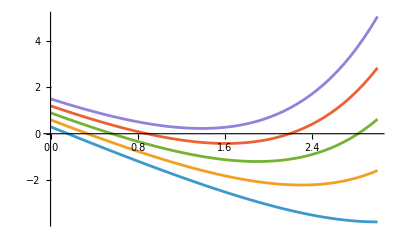

```mathematica
DSolve[D[y[t,x],t,t]==D[y[t,x],x]&&y[t,0]==Exp[-t^2],y,{t,x}]
```

{{y→Function[{t,x},ConditionalExpression[(ⅇ^(-t^2/(1+4 x)))/(√(4+1/x) √x), Re[1/x]≥-4]]}}

```mathematica
DSolve[D[y[t,x],t,t]==D[y[t,x],x]&&y[t,0]==Exp[-t^2],y[t,x],{t,x}]
```

{{y[t,x]→ConditionalExpression[(ⅇ^(-t^2/(1+4 x)))/(√(4+1/x) √x), Re[1/x]≥-4]}}

```mathematica
r=NDSolve[{x''[t]-Sin[x'[t]]==2,x[0]==1,x'[0]==2}, x,{t,-1,2}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
f=x/.r[[1,1]]
```

InterpolatingFunction[…]

```mathematica
f[1]
```

4.14277

```mathematica
f'[-.5]
```

0.564055

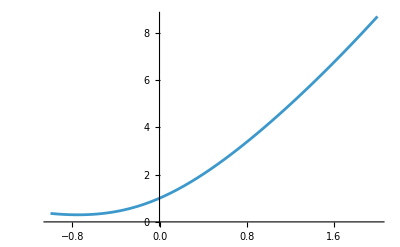

```mathematica
Plot[f[x],{x,-1,2}]
```

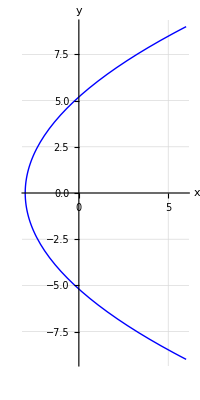

```mathematica
ParametricPlot[{t^2-3,3 t},{t,-3,3},PlotStyle->{Thick,Blue},AxesLabel->{"x","y"},GridLines->Automatic]
```

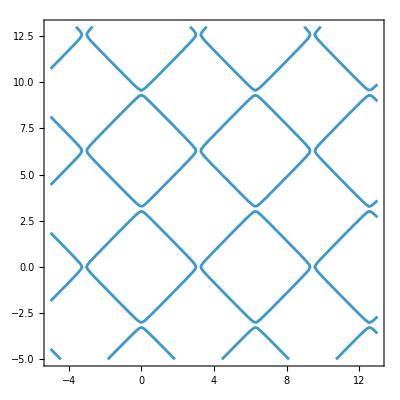

```mathematica
ContourPlot[Cos[x]+Cos[y] ==.01,{x,-5,13},{y,-5,13}]
```

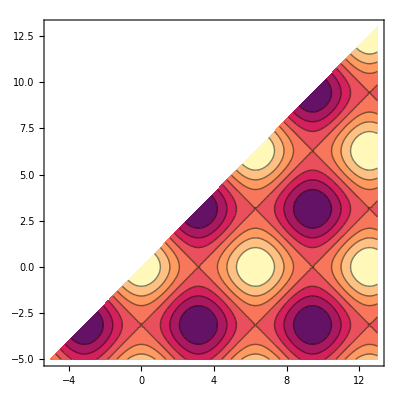

```mathematica
ContourPlot[(Cos[x]+Cos[y])&&(x-y>0),{x,-5,13},{y,-5,13}]
```

```mathematica
ly=Sin[RandomReal[{0,1},{10}]*10]
```

{0.918773,-0.922419,-0.212217,0.961716,-0.116451,0.477227,-0.4935,-0.714445,-0.449259,0.625136}

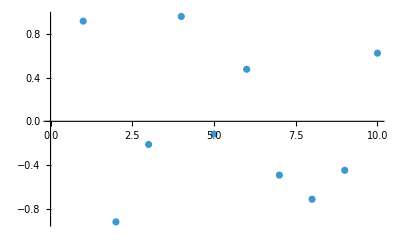

```mathematica
ListPlot[ly]
```

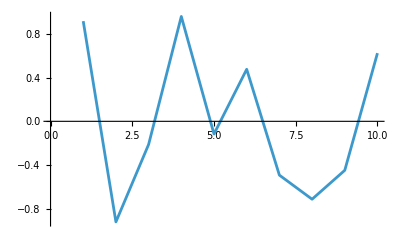

```mathematica
ListLinePlot[ly]
```

```mathematica
Plot3D[x^2-y^2,{x,-2,2},{y, -2,2}]
```

```mathematica
psi[t_]:=3/4*Exp[-I*8*t-1/2*t^2]
```

```mathematica
ParametricPlot3D[{t,Re[psi[t]],Im[psi[t]]},{t,-Pi,Pi}]
```

```mathematica
f1[x_]:=x^5
```

```mathematica
ParametricPlot3D[{Re[f1[u+I*v]], Im[f1[u+I*v]],v}, {u,-1,1},{v,-1,1}]
```

-Graphics3D-

```mathematica
g=3;
tor[{x_,y_,z_},R_,r_]:=(x^2+y^2+z^2)^2-2*(R^2+r^2)*(x^2+y^2)+2*(R^2-r^2)*z^2+(R^2-r^2)^2;
f3 = Product[tor[{x-1.5*Cos[i*2*Pi/g],y-1.5*Sin[i*2*Pi/g],z},1,1/4],{i,0,g-1}]-10;
ContourPlot3D[f3==0,{x,-3,3},{y,-3,3},{z,-1/2,1/2},PlotRange->{{-3,3},{-3,3},{-3,3}}]
```

-Graphics3D-

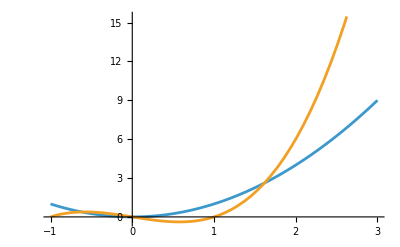

```mathematica
Plot[{x^2,x^3-x},{x,-1.,3.}]
```

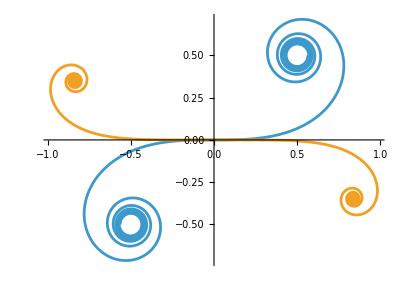

```mathematica
ParametricPlot[{{FresnelC[u],FresnelS[u]},{NIntegrate[Cos[t^4],{t,0,u}],-NIntegrate[Sin[t^4],{t,0,u}]}},{u,-5,5}]
```

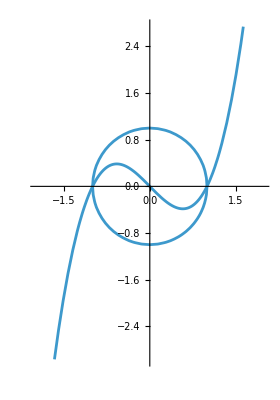

```mathematica
Show[{Plot[t^3-t,{t,-2,2}],ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2}]},AspectRatio->Automatic]
```

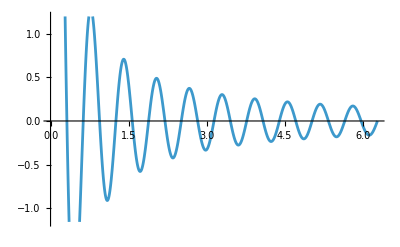

```mathematica
Plot[1/x*Sin[10*x],{x,0,2*Pi}]
```

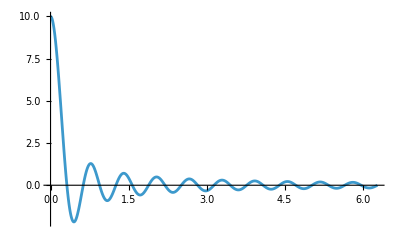

```mathematica
Plot[1/x*Sin[10*x],{x,0,2*Pi}, PlotRange->Full]
```

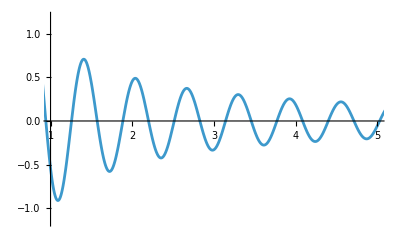

```mathematica
Plot[1/x*Sin[10*x],{x,0,2*Pi}, PlotRange->{{1,5}, Automatic}]
```

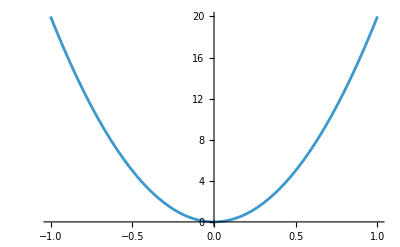
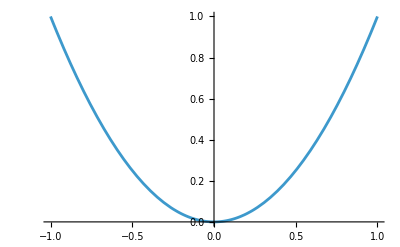

```mathematica
{Plot[20*x^2, {x,-1,1}], Plot[x^2, {x,-1,1}]}
```

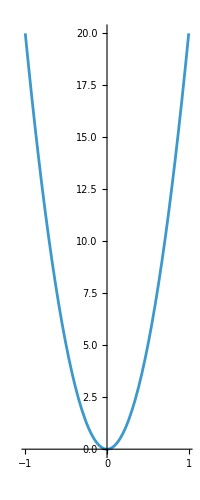
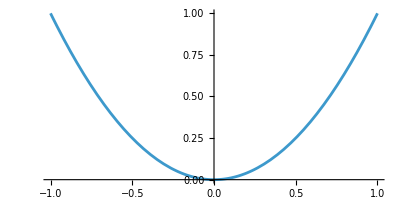

```mathematica
{Plot[20*x^2, {x,-1,1}, AspectRatio->Automatic], Plot[x^2, {x,-1,1},  AspectRatio->Automatic]}
```

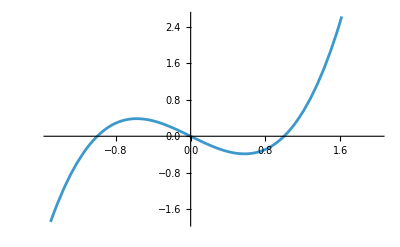

```mathematica
Plot[x^3-x,{x,-3/2,2}]
```

```mathematica
Plot[x^3-x,{x,-3/2,2}, GridLines->{{-1,1/2,1,3/2},{-1,1}}]
```

-Graphics-

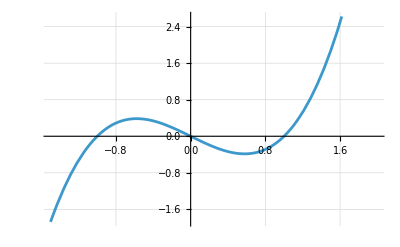

```mathematica
Plot[x^3-x,{x,-3/2,2}, GridLines->Automatic]
```

```mathematica
Plot[x^3-x,{x,-3/2,2}, GridLines->{Subdivide[-3/2, 2, 20], Subdivide[-2, 2, 20]}]
```

-Graphics-

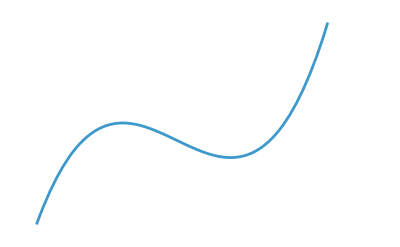

```mathematica
Plot[x^3-x,{x,-3/2,2}, Axes->False]
```

```mathematica
Plot[x^3-x,{x,-3/2,2}, Axes->{False, True}]
```

-Graphics-

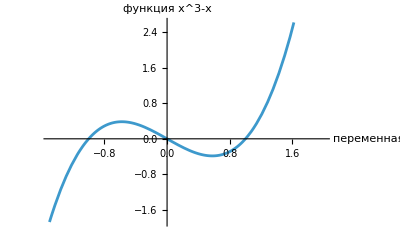

```mathematica
Plot[x^3-x,{x,-3/2,2}, AxesLabel->{"переменная","функция x^3-x"}]
```

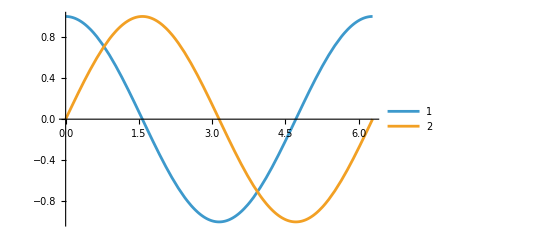

```mathematica
Plot[{Cos[x], Sin[x]},{x,0,2*Pi}, PlotLegends->Automatic]
```

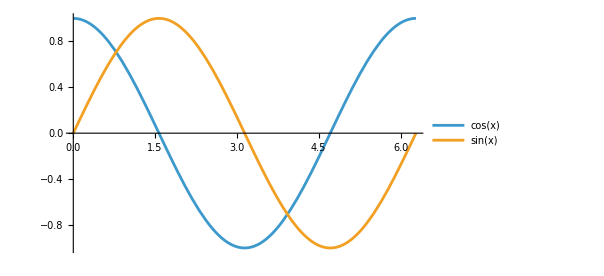

```mathematica
Plot[{Cos[x], Sin[x]},{x,0,2*Pi}, PlotLegends->"Expressions"]
```

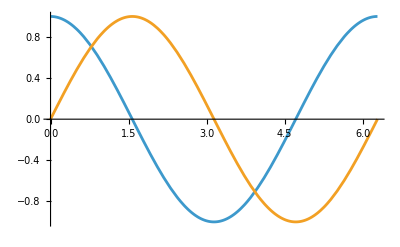

```mathematica
Plot[{Cos[x], Sin[x]},{x,0,2*Pi}, ImageSize->Scaled[2/3]]
```

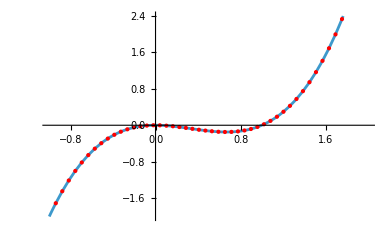

```mathematica
Plot[x^3-x^2, {x, -1,2}, Mesh->Full, MeshStyle->Red]
```

```mathematica
Plot[x^3-x^2, {x, -1,2}, Mesh->All, MeshStyle->Red]
```

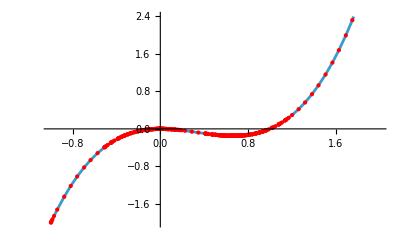

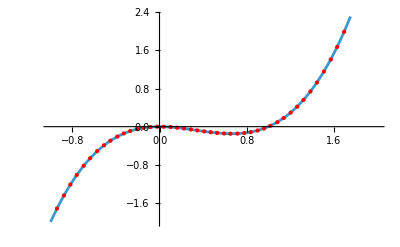

```mathematica
Plot[x^3-x^2, {x, -1,2}, Mesh->All, MeshStyle->Red, MaxRecursion->0]
```

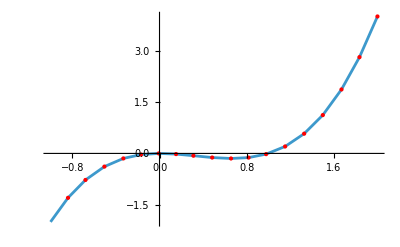

```mathematica
Plot[x^3-x^2, {x, -1,2}, Mesh->All, MeshStyle->Red, MaxRecursion->1, PlotPoints->10]
```

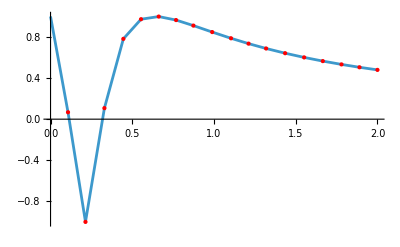
{0.015625,-Graphics-}

```mathematica
Timing@Plot[Sin[1/x], {x, 0,2}, Mesh->All, MeshStyle->Red, MaxRecursion->1, PlotPoints->10]
```

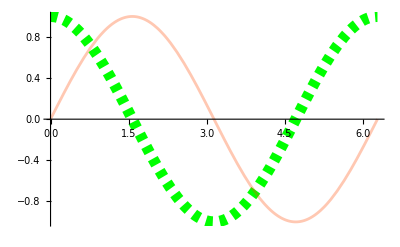

```mathematica
Plot[{Cos[x], Sin[x]},{x,0,2*Pi}, PlotStyle->{{Green, AbsoluteThickness[8], Dashed}, {RGBColor[1, 2/7,0], Opacity[0.3], Dashing}}]
```

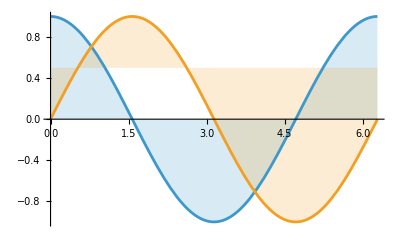

```mathematica
Plot[{Cos[x],Sin[x]},{x,0,2*Pi}, Filling->{1->Axis, 2->1/2}]
```

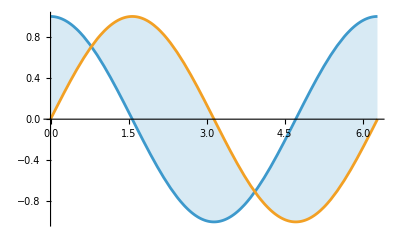

```mathematica
Plot[{Cos[x],Sin[x]},{x,0,2*Pi}, Filling->{1->{2}}]
```

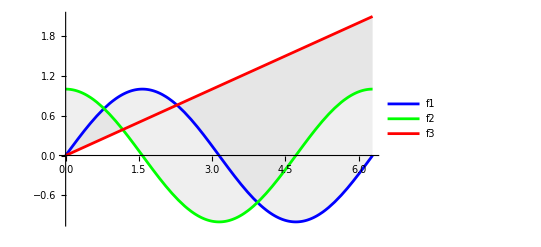

```mathematica
f1[x_]:=Sin[x]
f2[x_]:=Cos[x]
f3[x_]:=x/3

Plot[{f1[x],f2[x],f3[x]},{x,0,2 Pi},PlotStyle->{Blue,Green,Red},Filling->{{1->{3}},{2->{3}}},(*заполняем между первым и третьим графиком*)FillingStyle->Directive[LightGray,Opacity[0.4]],PlotLegends->{"f1","f2","f3"}]
```

```mathematica
2+x
a=123
s==t
```

2+x

123

s==t

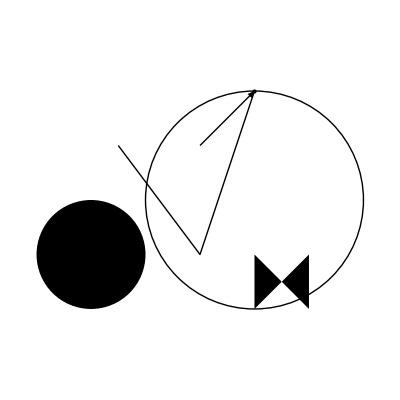

```mathematica
Graphics[{Point[{1,2}], Line[{{-3/2,1},{0,-1},{1,2}}], Circle[{1,0},2], Arrow[{{0,1},{1,2}}], Disk[{-2,-1},1], Polygon[{{1,-2},{2,-1},{2,-2},{1,-1}}]}, PlotRange->{{-3,3},{-3,3}}]
```

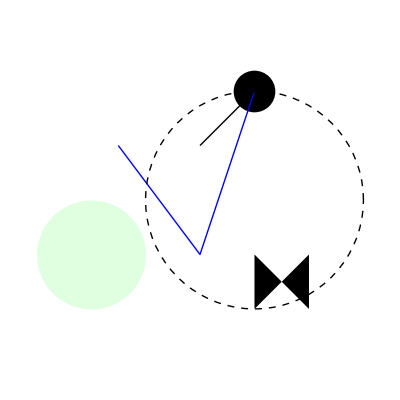

```mathematica
Graphics[{AbsolutePointSize[30],Point[{1,2}], {Blue, Line[{{-3/2,1},{0,-1},{1,2}}]}, {Dashed,Circle[{1,0},2]}, Arrow[{{0,1},{1,2}}], {LightGreen, Disk[{-2,-1},1]}, Polygon[{{1,-2},{2,-1},{2,-2},{1,-1}}]}, PlotRange->{{-3,3},{-3,3}}]
```

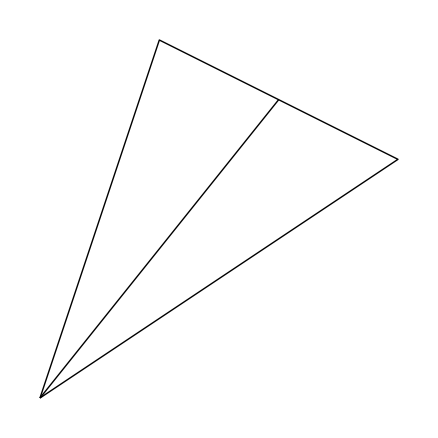

```mathematica
a={-1,-1};
b={2,1};
c={0,2};
Graphics[{Line[{a,b,c, a}], Line[{a, (b+c)/2}]}]
```

```mathematica
cs=Arrow[{{0,0,0},#*3}&/@Permutations[{1,0,0}]]
```

Arrow[{{{0,0,0},{3,0,0}},{{0,0,0},{0,3,0}},{{0,0,0},{0,0,3}}}]

```mathematica
Graphics3D[{cs,Sphere[{1,2,3},2], Cuboid[{-1,-1,-1}, {1,2,3}]}, PlotRange->{{-5,5},{-5,5},{-5,5}}]
```

-Graphics3D-

```mathematica
points = {{0,0,0},{1,0,0},{1/2, Sqrt[3]/2,0},{1/2, Sqrt[3]/6,1/Sqrt[2]}}
```

{{0,0,0},{1,0,0},{1/2,(√3)/2,0},{1/2,1/(2 √3),1/(√2)}}

```mathematica
tetrahedron = {Triangle[{1,2,3}], Triangle[{2,3,4}], Triangle[{3,4,1}], Triangle[{4,1,2}]};
Graphics3D[{GraphicsComplex[points, {tetrahedron}]}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Sin[a*x],{x,0,2*Pi}],{a,1,5}]
```

```mathematica
Manipulate[Plot[f[a*x],{x,0,2*Pi}],{a,1,5},{f,{Cos,Sin,Tan}}]
```

```mathematica
Manipulate[Plot[b*f[e],{x,0,2*Pi}, PlotRange->{Automatic, {-5,5}}],{{a,2},1,5,1},{{f,Sin},{Cos,Sin,Tan}}, {{b,2}, Subdivide[1/2,5,20]},{e,x}]
```

```mathematica
Manipulate[Plot[b*f[e],{x,0,2*Pi}, PlotRange->{Automatic, {-5,5}}],{a,1,5},{f,{Cos,Sin,Tan}}, {b, Subdivide[1/2,5,20]},{e,x}]
```

```mathematica
Manipulate[flag, {flag,{False, True}}]
```

```mathematica
n=3;
Manipulate[If[flag,n=Mod[(n+1),20]+3;
Pause[.2],n=3];
p=Table[{Cos[2*Pi*i/n],Sin[2*Pi*i/n]},{i,n+1}];
Graphics[{Line[p]}], {flag,{False, True}}]
```

```mathematica
Manipulate[{a,b,c}=pt;Graphics[{Circle[pt[[1]],2], Line[pt~Join~{pt[[1]]}], Line[{a,(b+c)/2}]}, PlotRange->{{-5,5}, {-5,5}}],{{pt,{{0,0},{1,0},{0,1}}},Locator}]
```

```mathematica
(*
if (condition){
//true
} else{
//false
}
*)
```

```mathematica
x=RandomInteger[{1,10}];
If[x>5,Print["икс больше ", x],
Print["маленькое ",x]]
```

маленькое3

```mathematica
x=10
While[x>5, Print[x];
Pause[0.5];
x=RandomInteger[{1,10}];
]
```

10

10

10

8

8

6

10

6

```mathematica
(*
for(инициализация;условие;изменение){
code
}
*)
```

```mathematica
For[i=0, i<=5,i++,Print[i];
Pause[0.5]]
```

0

1

2

3

4

5

```mathematica
Do[Print[i],{i, 5}(*от 1 до 5 с шагом 1*)]
```

1

2

3

4

5

```mathematica
Do[Print[i],{i, 1, 25,3}]
```

1

4

7

10

13

16

19

22

25

```mathematica
Do[Print[a],{a, {1,2,3,Sin,q,"Abc"}}]
```

1

2

3

Sin

q

Abc

```mathematica
x=.
Module[{y},y=4;Print[x," ",y," ",x+y]]
```

x 4 4+x

```mathematica
f[x_]:=Module[{n=30}, Do[If[i>x,Return[i]],{i,n}];x]
```

```mathematica
f[15]
```

15